```mathematica
EI=(H11+H22)/2+Sqrt[((H11-H22)/2)^2+H12*H21];
EII=(H11+H22)/2-Sqrt[((H11-H22)/2)^2+H12*H21];
a1=a2*H12/(EI-H11);
b1=b2*H21/(EII-H22);
a1
EI EII
```

```mathematica
Ecm[m_,m1_m2_]:=(m^2+m1^2-m2^2)/(2m);
mbe8=8.005305*931.5;
mbe8s=mbe8+18.15;
mhe4=3727.409;
mhe4s=mhe4+20.21;
mx=17.00;
mx=1.;
exbe8=(mbe8s^2+mx^2-mbe8^2)/(2*mbe8s);
exhe4=(mhe4s^2+mx^2-mhe4^2)/(2*mhe4s);
pxbe8=Sqrt[exbe8^2-mx^2];
pxhe4=Sqrt[exhe4^2-mx^2];

Print["ExBe8=",exbe8]   
Print["PxBe8=",pxbe8]
Print["ExHe4=",exhe4]    
Print["PxHe4=",pxhe4]
me= 0.00051099907*1000
```

ExBe8=18.128

PxBe8=18.1004

ExHe4=20.1556

PxHe4=20.1308

0.510999

4.42715×10^-6

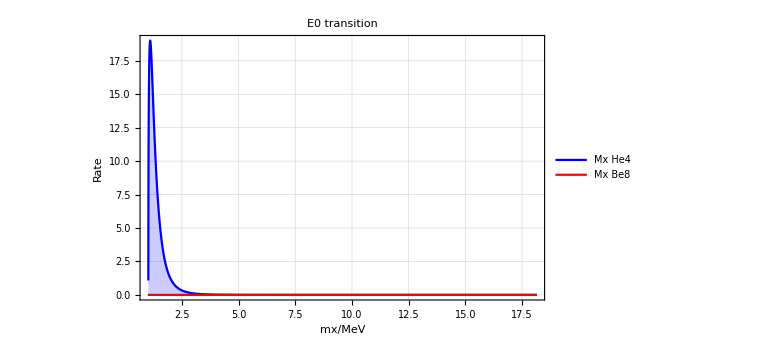

```mathematica
G[Ms_,M_,mx_]:=(Sqrt[((Ms^2-M^2+mx^2)/(2M))^2-mx^2])^1.5/mx^2*(Sqrt[1-4me^2/mx^2]/mx^4);
G[mhe4s,mhe4,15.]
Plot[{G[mhe4s,mhe4,x],G[mbe8s,x,mbe8]},{x,1,mbe8s-mbe8},PlotRange->{{0,mhe4s-mhe4},{0,All}},
Frame->True,
FrameLabel->{"mx/MeV","Rate"},
PlotLabel->"E0 transition",
PlotLegends->Placed[{"Mx He4","Mx Be8"},Center],
LabelStyle->{ FontSize->20,Black},
Filling->Axis,
PlotStyle->{Blue,Red,Green},
GridLines->Automatic,
ImageSize->Large]
```

```mathematica
d=(mhe4s-mhe4);
En[q2_]:=(d-Sqrt[d^2-q2])/2;
En'[q2]
4*En[q2]*d-4En[q2]^2
G[q2_]=-(-d+q2)/(4*Sqrt[d^2-q2]);
G[q2]
```

1/(4 √(408.444-q2))

40.42 (20.21-√(408.444-q2))-(20.21-√(408.444-q2))^2

(20.21-q2)/(4 √(408.444-q2))

0.127874

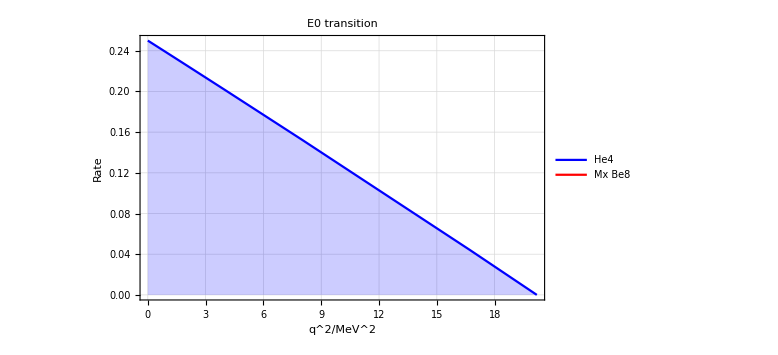

```mathematica
G[10]
Plot[{G[q2],-Sqrt[d^2-q2]/4},{q2,0,(mhe4s-mhe4)^2},PlotRange->{{0,(mhe4s-mhe4)^2},{0,All}},
Frame->True,
FrameLabel->{"q^2/MeV^2","Rate"},
PlotLabel->"E0 transition",
PlotLegends->Placed[{"He4","Mx Be8"},Center],
LabelStyle->{ FontSize->20,Black},
Filling->Axis,
PlotStyle->{Blue,Red},
GridLines->Automatic,
ImageSize->Large]
```

-23.3246

20.1688

151070.

2*mhe4s*Ecm[mhe4s,10.,mhe4]=151170.

406.754

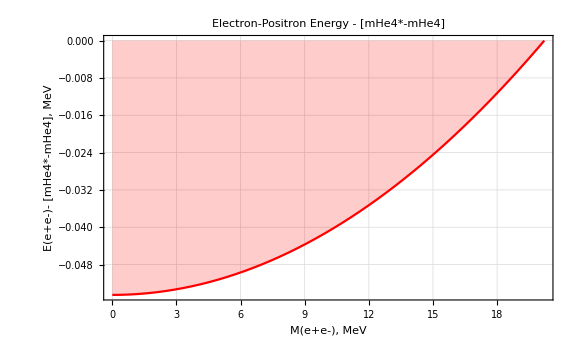

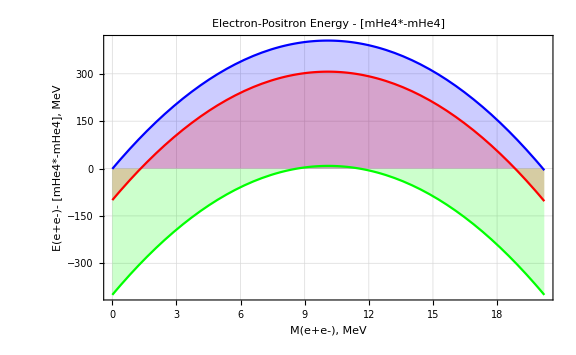

3747.62

3727.41

20.21

-0.041152

0.510999

```mathematica
Ecm[m_,m1_m2_]:=(m^2+m1^2-m2^2)/(2m);
mbe8=8.005305*931.5;
mbe8s=mbe8+18.15;
mhe4=3727.409;
mhe4s=mhe4+20.21;
me= 0.00051099907*1000;
mx=17.00;
mx=1.;
exbe8=(mbe8s^2+mx^2-mbe8^2)/(2*mbe8s);
exhe4=(mhe4s^2+mx^2-mhe4^2)/(2*mhe4s);
pxbe8=Sqrt[exbe8^2-mx^2];
pxhe4=Sqrt[exhe4^2-mx^2];

Print["ExBe8=",exbe8]   
Print["PxBe8=",pxbe8]
Print["ExHe4=",exhe4]    
Print["PxHe4=",pxhe4]


Ecm[m_,m1_,m2_]:=(m^2+m1^2-m2^2)/(2m);
UnI[m_,m1_,m2_,ee_]:=m^2-m2^2-2m*Ecm[m,m1,m2]+4*ee(Ecm[m,m1,m2]-ee);
U1[m_,m1_,m2_,ee_]:=m^2-m2^2;
U2[m_,m1_,m2_,ee_]:=2*m^2*Ecm[m,m1,m2];
U3[m_,m1_,m2_,ee_]:=4*ee(Ecm[m,m1,m2]-ee);
UnI[mhe4s,10.,mhe4,1.]
Ecm[mhe4s,10.,mhe4]
Print[mhe4s^2-mhe4^2]
Print["2*mhe4s*Ecm[mhe4s,10.,mhe4]=", 2*mhe4s*Ecm[mhe4s,10.,mhe4]]
4*10(Ecm[mhe4s,10,mhe4]-10)
Plot[Ecm[mhe4s,q,mhe4]-(mhe4s-mhe4),{q,0,(mhe4s-mhe4)},
PlotRange->All,
Frame->True,
FrameLabel->{"M(e+e-), MeV","E(e+e-)- [mHe4*-mHe4], MeV"},
PlotLabel->"Electron-Positron Energy - [mHe4*-mHe4]",
LabelStyle->{ FontSize->20,Black},
Filling->Axis,
PlotStyle->{Blue,Red},
GridLines->Automatic,
ImageSize->Large]
Plot[{UnI[mhe4s,2*me,mhe4,ee],
UnI[mhe4s,20.,mhe4,ee],
UnI[mhe4s,10.,mhe4,ee]},{ee,0,(mhe4s-mhe4)},
PlotRange->All,
Frame->True,
FrameLabel->{"M(e+e-), MeV","E(e+e-)- [mHe4*-mHe4], MeV"},
PlotLabel->"Electron-Positron Energy - [mHe4*-mHe4]",
LabelStyle->{ FontSize->20,Black},
Filling->Axis,
PlotStyle->{Blue,Green,Red},
GridLines->Automatic,
ImageSize->Large]
mhe4s
mhe4
mhe4s-mhe4
k=10; Ecm[mhe4s,k,mhe4]-(mhe4s-mhe4)
me
```

```mathematica
(m
```

```mathematica
me
```

0.510999

```mathematica
2*mhe4s^2*Ecm[mhe4s,0.,mhe4]
```

5.66154×10^8

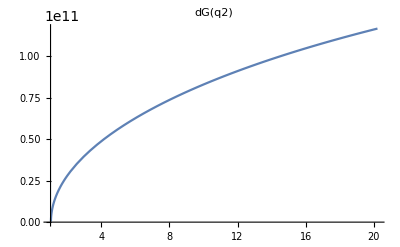

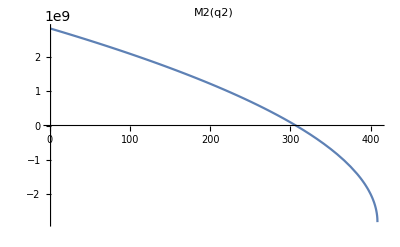

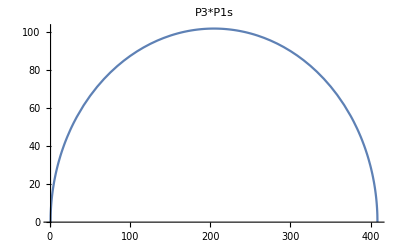

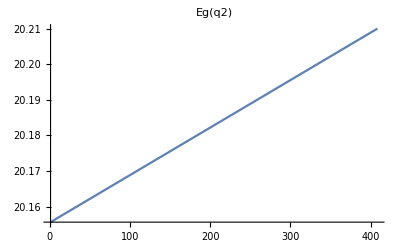

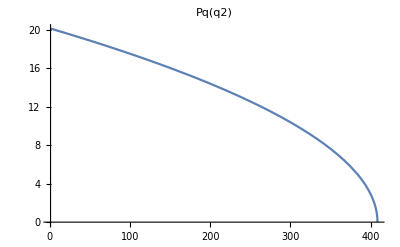

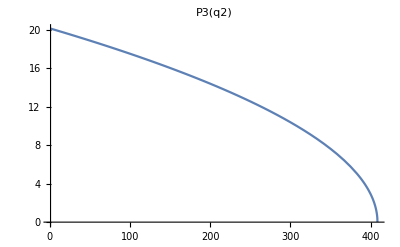

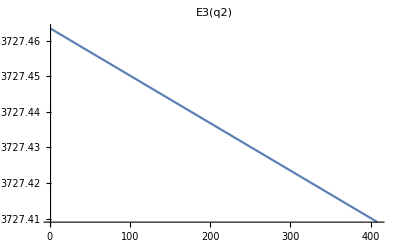

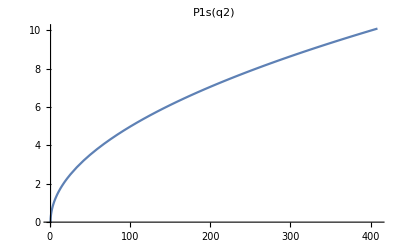

```mathematica
mbe8=8.005305*931.5;
mbe8s=mbe8+18.15;
mhe4=3727.409;
mhe4s=mhe4+20.21;
me= 0.00051099907*1000;

Eq[m_,m3_,q2_]:=(m^2-m3^2+q2)/(2m);
Pq[m_,m3_,q2_]:=Sqrt[Eq[m,m3,q2]^2-q2];
P3[m_,m3_,q2_]:=Pq[m,m3,q2];
E3[m_,m3_,q2_]:=Sqrt[P3[m,m3,q2]^2+m3^2];
P1s[q2_]:=Sqrt[q2/4-me^2];
gamma[m_,m3_,q2_]:=Eq[m,m3,q2]/Sqrt[q2];
vel[m_,m3_,q2_]:=Sqrt[Eq[m,m3,q2]^2-q2]/Eq[m,m3,q2];
p3q[m_,m3_,q2_]:=(m^2-m3^2-q2)/2.;
p1q[q2_]:=q2/2.;
p3p1[m_,m3_,q2_]:=m*gamma[m,m3,q2]*vel[m,m3,q2]*Sqrt[q2]/2;
M2[m_,m3_,q2_]:=2*p3p1[m,m3,q2]*(p3q[m,m3,q2]-p3p1[m,m3,q2])-m3^2*(p1q[q2]-me^2)-me^2*m3^2;
q2min=(2me)^2;
q2max=(mhe4s-mhe4)^2;
dG[m_,m3_,q2_]:=M2[m,m3,q2]*P3[m,m3,q2]*P1s[q2];

Plot[dG[mhe4s,mhe4,q2],                   {q2,2me,mhe4s-mhe4},PlotLabel->"dG(q2)"]
Plot[M2[mhe4s,mhe4,q2],                   {q2,q2min,q2max},PlotLabel->"M2(q2)"]
Plot[P3[mhe4s,mhe4,q2]*P1s[q2], {q2,q2min,q2max},PlotLabel->"P3*P1s"]
Plot[Eq[mhe4s,mhe4,q2],                 {q2,q2min,q2max},PlotLabel->"Eg(q2)"]
Plot[Pq[mhe4s,mhe4,q2],                  {q2,q2min,q2max},PlotLabel->"Pq(q2)"]
Plot[P3[mhe4s,mhe4,q2],                   {q2,q2min,q2max},PlotLabel->"P3(q2)"]
Plot[E3[mhe4s,mhe4,q2],                   {q2,q2min,q2max},PlotLabel->"E3(q2)"]
Plot[P1s[q2],                                             {q2,q2min,q2max},PlotLabel->"P1s(q2)"]
Plot[gamma[mhe4s,mhe4,q2],             {q2,q2min,q2max},PlotLabel->"gamma(q2)"]
Plot[vel[mhe4s,mhe4,q2],                  {q2,q2min,q2max},PlotLabel->"vel(q2)"]
Plot[p3q[mhe4s,mhe4,q2],                  {q2,q2min,q2max},PlotLabel->"p3q(q2)"]
Plot[p1q[q2],                                             {q2,q2min,q2max},PlotLabel->"p1q(q2)"]
```

```mathematica
me
```

0.000510999

```mathematica
Sqrt[300.]
(* M2[m_,m3_,q2_]:=2*p3p1[m,m3,q2]*(p3q[m,m3,q2]-p3p1[m,m3,q2])-m3^2*(p1q[q2]-me^2)-me^2*m3^2; *)
mx=20.^2;
M2[mhe4s,mhe4,mx^2]
a=2*p3p1[mhe4s,mhe4,mx]
b=(p3q[mhe4s,mhe4,mx]-p3p1[mhe4s,mhe4,mx])
c=2*p3p1[mhe4s,mhe4,mx]*(p3q[mhe4s,mhe4,mx]-p3p1[mhe4s,mhe4,mx])
mhe4^2*(p1q[mx]-me^2)
me^2*mhe4^2
d=mhe4^2*(p1q[mx]-me^2)+me^2*mhe4^2
```

17.3205

-9.96741×10^6-6.65689×10^9 ⅈ

10860.7

69904.8

7.59215×10^8

2.77509×10^9

3.62789×10^6

2.77872×10^9

```mathematica
c
d
c-d
```

7.59215×10^8

2.77872×10^9

-2.0195×10^9